```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
cef={ChartElementData["BoxWhisker"][##],EdgeForm[],FaceForm[None],ChartElementData["PointDensity","PointStyle"->Directive[EdgeForm[Black],Opacity[.6],PointSize[.03],Darker[Charting`ChartStyleInformation["Color"]]]][##]}&;
```

```mathematica
EWa = Flatten@Import["data_FigS13/EWSac.csv"];
EWv = Flatten@Import["data_FigS13/EWSvar.csv"];
```

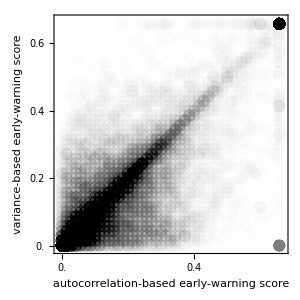

```mathematica
AcVarEWS=Show[ListPlot[Transpose@{EWa,EWv},
PlotStyle->{Black,Opacity[.009],PointSize[.03]},
Frame->True,
AspectRatio->1,
ImageSize->300,
FrameTicksStyle->12,
PlotRange->{{-.01,.67},{-.01,.67}},
FrameLabel->{{"variance-based early-warning score",None},{"autocorrelation-based early-warning score",None}},
LabelStyle->12,
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1,0.2],None}}]]
```

```mathematica
Ccof = Flatten@Import["data_FigS13/corrcof.csv"];
Cpv = Flatten@Import["data_FigS13/corrp.csv"];
```

```mathematica
SpearmanRankTest[EWa,EWv,"TestDataTable"]
```

General::munfl: 2.6701674983140383709738×10^-3071 is too small to represent as a normalized machine number; precision may be lost.

| Statistic | P-Value
Spearman Rank | 0.730181 | 0.

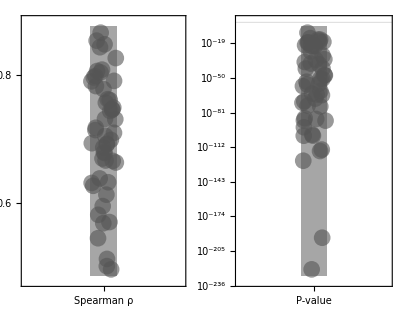

```mathematica
corrpl=GraphicsRow[{
BoxWhiskerChart[Ccof,"Outliers",
ChartLabels->{"Spearman ρ"},ChartStyle->Gray,ChartElementFunction->cef,
Frame->True,
(*FrameStyle->Black,*)
FrameTicks->{{Range[0,1,0.1],None},{None,None}},
FrameTicksStyle->12,
AspectRatio->GoldenRatio],
BoxWhiskerChart[Cpv,ChartLabels->{"P-value"},ChartStyle->Gray,ChartElementFunction->cef,
Frame->True,
GridLines->{{},{.001}},
(*FrameStyle->Black,*)
FrameTicks->{{Automatic,None},{None,None}},
FrameTicksStyle->12,
AspectRatio->GoldenRatio,
ScalingFunctions->"Log"]}, ImageSize->400]
```